## Limit Cycles

```mathematica
DynamicViscosity = 1/1000; (*kg/(m·s)*)
DensityWater = 1000; (*kg/m.b3*)
(* Following equations from Motion planning for Multiple Millimeter-scale Magnetic Capsules in a Fluid Environment http://robotics.tch.harvard.edu/publications/pdfs/vartholomeos2012motion.pdf*)
ReynoldsNum[vel_,rad_]:=If[vel==0,100,vel (DensityWater (2 rad))/DynamicViscosity]
DragCoeff[vel_,rad_]:=Module[{Re = ReynoldsNum[vel,rad]}, 4/10+6/(1+√Re)+24/Re]
ForceDrag[rad_,vel_]:= -1/2 DensityWater DragCoeff[vel,rad] (π rad^2) vel^2
ForceMag[rad_,grad_]:=4/3 π rad^3 Msat grad
massCapsule[rad_]:=4/3 π rad^3 DensityFerrous;
DensityFerrous = 7850;(*kg/m^3*)
DensityCapsule = 1174;
Msat = 1.36 10^6;(*A/m, from An MRI-powered and controlled actuator technology for tetherless robotic interventions *)
μ0 = 4π 10^-7;
magMoment[rad_] := 4/3 π rad^3 Msat (*A m^2*)
Fk[rk_,ri_,mk_,mi_]:= Module[{nik },If[Norm[rk-ri]<=$MachineEpsilon,{0,0},

nik = (rk-ri)/Norm[rk-ri];μ0/(4π)1/Norm[rk-ri]^4(-15 nik ((mk.nik)(mi.nik))+3 nik(mk.mi)+3(mk(mi.nik)+mi(mk.nik)))]]
plotMagnet[rad_]:= {Lighter[Gray],Disk[{0,0},rad],Darker[Red],Disk[{0,0},rad,{0,Pi}],Black,Circle[{0,0},rad]};
Fksimple[rk_,ri_,mk_,mi_]:=μ0/(4π)1/Norm[rk-ri]^4(-15 (rk-ri)/Norm[rk-ri] ((mk.((rk-ri)/Norm[rk-ri]))(mi.((rk-ri)/Norm[rk-ri])))+3 (rk-ri)/Norm[rk-ri](mk.mi)+3(mk(mi.((rk-ri)/Norm[rk-ri]))+mi(mk.((rk-ri)/Norm[rk-ri]))))
```

## Make Plots of max Vel as func of time

```mathematica
radVals = Table[r,{r,0.001,0.005,0.001}];
pt =Table[Table[a=Solve[ForceDrag[rad1,vel]+ForceMag[rad1,m]==0,vel,Reals]; {m,a⟦1,1,2⟧},{m,0,0.04,0.04/80}],{rad1,radVals}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

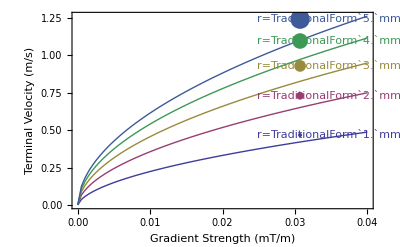

```mathematica
ListPlot[pt,
Frame->{{True,False},{True,False}},PlotStyle->Thick,FrameLabel-> {"Gradient Strength (mT/m)","Terminal Velocity (m/s)"},
Joined->True,
Epilog-> Table[pos = {-0.0053,-.02}+pt⟦i,-1,;;⟧;{ColorData[1,i],PointSize[7radVals⟦i⟧],Point[pos-{0.004,0}],Text[ StringForm["r=``mm",1000radVals⟦i⟧], pos]},{i,Length[pt⟦;;,-1,-1⟧]}]]
```

## Plot Reynolds number as function of velocity and radius

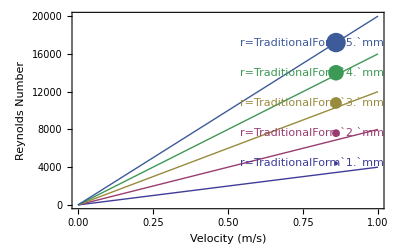

```mathematica
radVals = Table[r,{r,0.001,0.005,0.001}];
Plot[Evaluate[Table[ReynoldsNum[vel,2rad1],{rad1,radVals}]],{vel,0,1},PlotStyle->Thick,
Frame->{{True,False},{True,False}},PlotStyle->Thick,FrameLabel-> {"Velocity (m/s)","Reynolds Number"},Epilog-> Table[
pos ={0.78,ReynoldsNum[0.8,2radVals⟦i⟧]+1200};{ColorData[1,i],PointSize[7radVals⟦i⟧],Point[pos+{0.08,0}],
Text[ StringForm["r=``mm",1000radVals⟦i⟧],pos]},{i,Length[radVals]}]]
```

## Step response (shows steady-state velocity) to a gradient field input

```mathematica
radVals = Table[r,{r,0.001,0.005,0.001}];
Tmax = .5;
s=Table[NDSolve[{v'[t]==1/massCapsule[rad1](ForceDrag[rad1,v[t]]+ForceMag[rad1,0.04]),v[0]==0},v,{t,0,Tmax}],{rad1,radVals}]
```

{{{v→InterpolatingFunction[{{0.,0.5}},<>]}},{{v→InterpolatingFunction[{{0.,0.5}},<>]}},{{v→InterpolatingFunction[{{0.,0.5}},<>]}},{{v→InterpolatingFunction[{{0.,0.5}},<>]}},{{v→InterpolatingFunction[{{0.,0.5}},<>]}}}

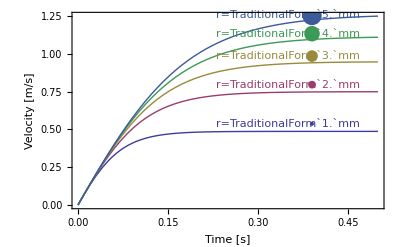

```mathematica
Plot[Evaluate[v[t]/.s],{t,0,Tmax},PlotRange->All,PlotStyle->Thick,
Frame->{{True,False},{True,False}},FrameLabel-> {"Time [s]","Velocity [m/s]"},Epilog-> Table[pos =  {0,+.05}+Prepend[Evaluate[v[Tmax.7]/.s⟦i⟧],.7 Tmax];{ColorData[1,i],PointSize[7radVals⟦i⟧],Point[pos+{0.04,0}],Text[ StringForm["r=``mm",1000radVals⟦i⟧],pos]},{i,Length[radVals]}]]
```

## Simple limit cycle: pulling along z axis (we can’t pull along other axis very well since attraction is dominated by z component. Bigger particle moves faster

Vel1 =  ForceMag[rad1, grad] -  ForceDrag[radshell, vel] - Fk[{0, 0}, {0, r}, {0, magMoment[rad1]}, {0, magMoment[rad2]}];
Vel2 =  ForceMag[rad2, grad] -  ForceDrag[radshell, vel] + Fk[{0, 0}, {0, r}, {0, magMoment[rad1]}, {0, magMoment[rad2]}];
Vel1 == Vel2,  what is r?

```mathematica
FullSimplify[ForceMag[rad1,grad]- ForceMag[rad2,grad]  ==2Simplify[Fksimple[{0,0},{0,r},{0,magMoment[rad1]},{0,magMoment[rad2]}]⟦2⟧]]
```

grad (5.69675×10^6 rad1^3-5.69675×10^6 rad2^3)==(r^2 rad1^3 rad2^3 (1.55774×10^8 r-1.16831×10^8 Re[r]))/Abs[r]^7

```mathematica
Solve[grad (5.6967546785094915*^6 rad1^3-5.6967546785094915*^6 rad2^3)==(r^2 rad1^3 rad2^3 (1.5577446656217495*^8 r-1.168308499216312*^8 Re[r]))/Abs[r]^7,{grad}]
```

{{grad→(1. r^2 rad1^3 rad2^3 (1.55774×10^8 r-1.16831×10^8 Re[r]))/((5.69675×10^6 rad1^3-5.69675×10^6 rad2^3) Abs[r]^7)}}

```mathematica
Solve[grad (5.6967546785094915*^6 rad1^3-5.6967546785094915*^6 rad2^3)==(r^2 rad1^3 rad2^3 (1.5577446656217495*^8 r-1.168308499216312*^8 r))/r^7,{r}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→-(1.61697 rad1^(3/4) rad2^(3/4))/((grad rad1^3-1. grad rad2^3)^(1/4))},{r→-((0.+1.61697 ⅈ) rad1^(3/4) rad2^(3/4))/((grad rad1^3-1. grad rad2^3)^(1/4))},{r→((0.+1.61697 ⅈ) rad1^(3/4) rad2^(3/4))/((grad rad1^3-1. grad rad2^3)^(1/4))},{r→(1.61697 rad1^(3/4) rad2^(3/4))/((grad rad1^3-1. grad rad2^3)^(1/4))}}

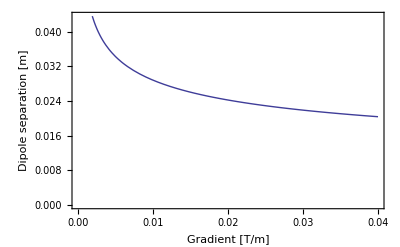

```mathematica
Plot[(1.6169708507909912 rad1^(3/4) rad2^(3/4))/((grad rad1^3-1. grad rad2^3)^(1/4))/.{rad1->0.005,rad2->0.001},{grad,0.0001,0.04},AxesOrigin->{0,0},Frame->{{True,False},{True,False}},PlotStyle->Thick,FrameLabel-> {"Gradient [T/m]","Dipole separation [m]"}]
```

```mathematica
radVals = {0.001,0.002,0.003,0.004};
seperationDist[rad1_,rad2_,grad_]:=(1.6169708507909912 rad1^(3/4) rad2^(3/4))/((grad rad1^3-1. grad rad2^3)^(1/4))
Plot[Evaluate[Table[seperationDist[rad1,rad2,grad]/.{rad1->0.005},{rad2,radVals}]],{grad,0.0001,0.04},AxesOrigin->{0,0},Frame->{{True,False},{True,False}},PlotStyle->Thick,FrameLabel-> {"Gradient [T/m]","Dipole separation d [m]"},
Epilog-> {gradv = 0.03;Black,PointSize[7 0.005],Point[{gradv+0.004,0}],
 Table[
pos ={gradv,0.005+seperationDist[rad1,radVals⟦i⟧,gradv]/.{rad1->0.005}};
{If[i==1,{Arrowheads[{-.03,.03}],Arrow[{{gradv+0.005,0},pos+{0.005,0}}], Text["d",{gradv+0.006,pos⟦2⟧/2}]}],
ColorData[1,i],PointSize[7radVals⟦i⟧],Point[pos+{0.004,0}],
Text[ StringForm["r_2=``mm",1000radVals⟦i⟧],pos]},{i,Length[radVals]}]
}
]
```

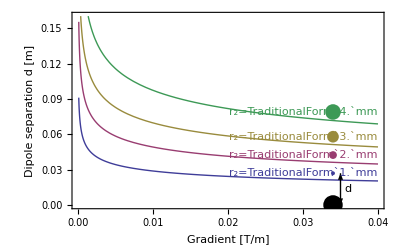

```mathematica
RotationMatrix[π/4,{0,1,0}]//MatrixForm
N[RotationMatrix[π/4,{0,1,0}]]//MatrixForm
```

(1/(√2) | 0 | 1/(√2)
0 | 1 | 0
-1/(√2) | 0 | 1/(√2))

(0.707107 | 0. | 0.707107
0. | 1. | 0.
-0.707107 | 0. | 0.707107)

```mathematica
RotationMatrix[{{1,0,0},Normalize[{1,1,1}]}]//MatrixForm
N[RotationMatrix[{{1,0,0},Normalize[{1,1,1}]}]]//MatrixForm
```

(1/(√3) | -1/(√3) | -1/(√3)
1/(√3) | 1/6 (3+√3) | 1/6 (-3+√3)
1/(√3) | 1/6 (-3+√3) | 1/6 (3+√3))

(0.57735 | -0.57735 | -0.57735
0.57735 | 0.788675 | -0.211325
0.57735 | -0.211325 | 0.788675)